```mathematica
<<Geometry`
```

## TEST1

### Case 1

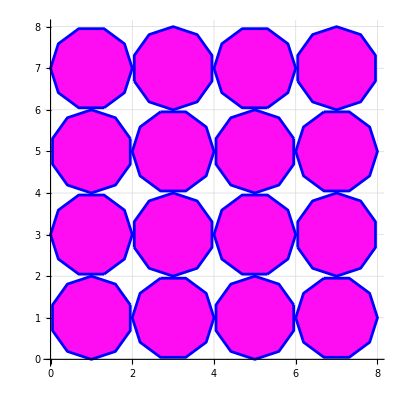

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[10,RGBColor[1,.05,.95,.1]][[1]],{1,1}],{Blue,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr1
```

### Case 2

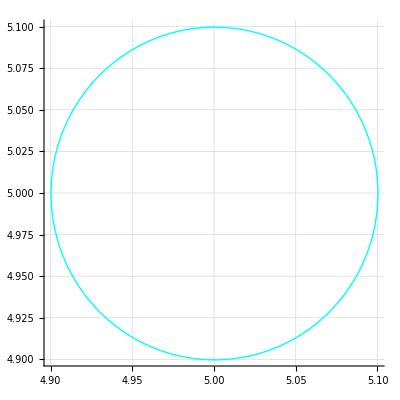

```mathematica
cCircle[{5,5},.1]//toGL//gr1
```

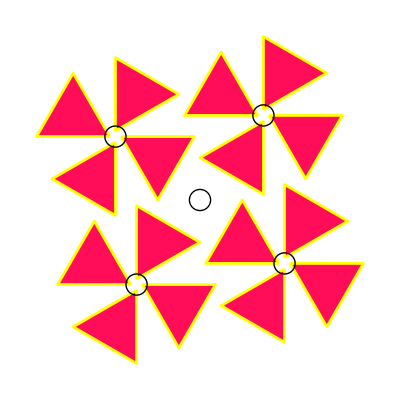

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr
```

## TEST2

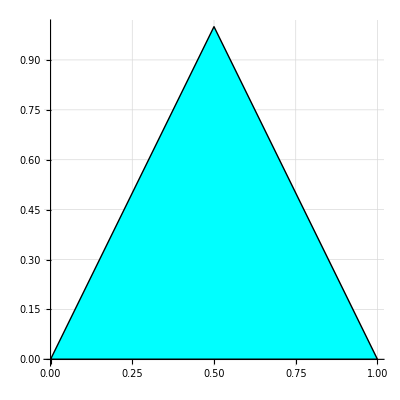

```mathematica
{{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0, 1, 1],1}},{GrayLevel[0],1,0.0025,2 π,2 π}}//toGL//gr1
```

```mathematica
sym4rot[figke_]:= Module[{rotp},
rotp={1,1};
tra3[Scale[{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]},.5],{-.5,-.5}]
]
sym4ref[figke_]:= Module[{rotp},
rotp={1,1};
tra3[Scale[{figke,ref3[figke,{{1,0},rotp}],rot3[figke,{π,rotp}],ref3[figke,{{0,1},rotp}]},.5],{-.5,-.5}]
]
dpoly:={{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.0025,2 π,2 π}}
dpoly:={{{{1,{{0.0,0.4},{0.5,0.0},{0.5,0.5},{1.0,0.75},{0.5,1.0},{0.0,0.6}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.005,2 π,2 π}}}
Nest[sym4ref,dpoly,4]//toGL//gr
```

-Graphics-

```mathematica
dpoly:={{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.0025,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.7,0.2},{1,1},{0,1}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
sym4rot[sym4ref[sym4rot[sym4rot[dpoly]]]]//toGL//gr
```

-Graphics-

## TEST3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},2]
```

```mathematica
dpoly:={{{1,{{0,0},{0.7,0.2},{1,1},{0,1}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,1},{0.25,1},{0,0.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
```

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## temp-1

```mathematica
dpoly:={{{1,{{0,0},{0.7,0.2},{1,1},{0,1}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,1},{0.25,1},{0,0.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
```

```mathematica
ArcSin[1/(√10)] 180./π
ArcCos[3/(√10)] 180./π
ArcTan[1/3] 180./π
```

18.4349

18.4349

18.4349

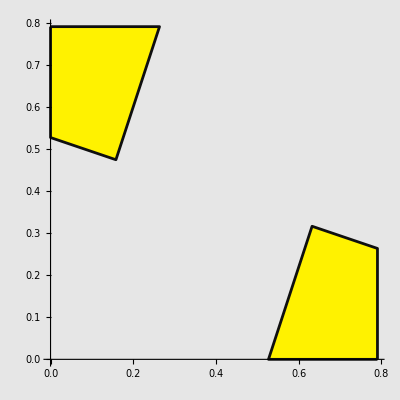

```mathematica
dpoly:={{{1,{{0.75,0.25},{2./3,0.5},{0.5,0.5},{0.5,1./6}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly2:=rot3[{dpoly,rot3[dpoly,{π,{0.25,0.5}}]},{-ArcTan[1/3],{0,0}}]
dpoly2//toGL//gr2
```

## temp-2

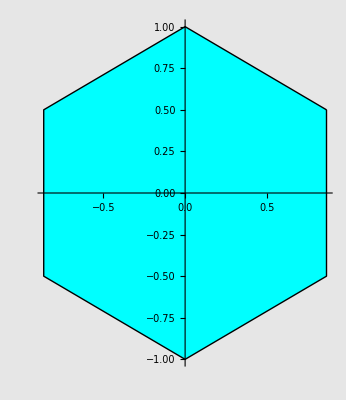

```mathematica
newGeo[6]//toGL//gr2
```

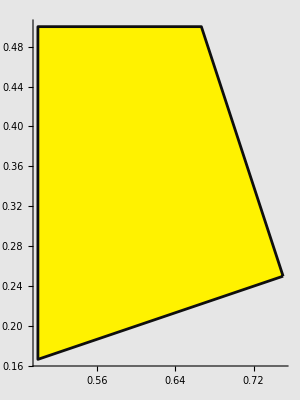

```mathematica
dpoly:={{{1,{{0.75,0.25},{2./3,0.5},{0.5,0.5},{0.5,1./6}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly//toGL//gr2
tra3[dpoly,{-.5,-1./6}]//toGL//gr2;
sca2pnt[tra3[dpoly,{-.5,-1./6}],{{0,0},1/√((.25)^2+(.75)^2)}]//toGL//gr2;
sca2pnt[dpoly,{{.5,1./6},1/√((.25)^2+(.75)^2)}]//toGL//gr2;
```

```mathematica
newGeo[4]
```

{{{1,{{1/(√2),1/(√2)},{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)},{1/(√2),-1/(√2)}}},{RGBColor[0, 1, 1],1}},{GrayLevel[0],1,0.0025,2 π,2 π}}

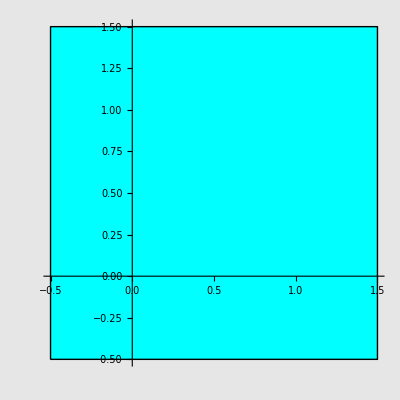

```mathematica
sca2pnt[{{{1,{{0,0},{.5,0},{.5,.5},{0,.5}}},{RGBColor[0, 1, 1],1}},{GrayLevel[0],1,0.0025,2 π,2 π}},{{.5,.5},1}]//toGL//gr2
```